## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.6, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL06=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.6)
```

0.599871

```mathematica
Zprime10decayfixedmass06[CvR_]:=MassZprime10/(12π)(1/4(CvL06+CvR)^2+1/4(CvL06-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL06+CvR)^2-1/2(CvL06+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass06Table=Table[{Q[i],Zprime10decayfixedmass06[Q[i]]},{i,0,Npt}]
```

{{0.,47.7116},{0.1,49.0359},{0.2,53.012},{0.3,59.6399},{0.4,68.9196},{0.5,80.851},{0.6,95.4343},{0.7,112.669},{0.8,132.556},{0.9,155.095},{1.,180.285}}

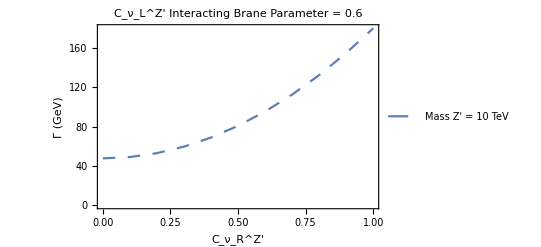

```mathematica
PlotZprimeDecayFixed1006=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass Z' = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z'  Interacting Brane Parameter = 0.6"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

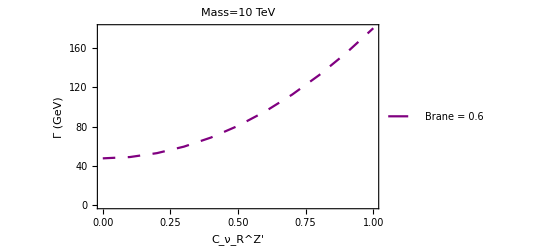

```mathematica
PlotZprimeDecayFixed1006B=ListPlot[%%, Joined-> True,PlotStyle->{Purple,Dashing[Medium]},PlotLegends->{"Brane = 0.6"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass06Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 47.7116
0.1 | 49.0359
0.2 | 53.012
0.3 | 59.6399
0.4 | 68.9196
0.5 | 80.851
0.6 | 95.4343
0.7 | 112.669
0.8 | 132.556
0.9 | 155.095
1. | 180.285

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.6, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL06=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.6)
```

0.599871

```mathematica
Zprime8decayfixedmass06[CvR_]:=MassZprime8/(12π)(1/4(CvL06+CvR)^2+1/4(CvL06-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL06+CvR)^2-1/2(CvL06+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass06Table=Table[{Q[i],Zprime8decayfixedmass06[Q[i]]},{i,0,Npt}]
```

{{0.,38.1629},{0.1,39.2214},{0.2,42.401},{0.3,47.7017},{0.4,55.1235},{0.5,64.6663},{0.6,76.3302},{0.7,90.1152},{0.8,106.021},{0.9,124.048},{1.,144.197}}

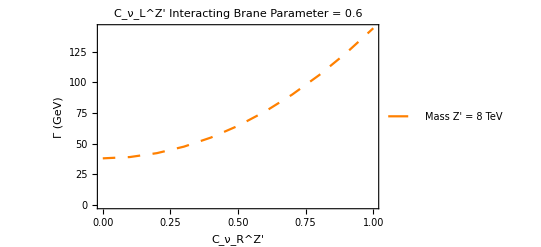

```mathematica
PlotZprimeDecayFixed806=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass Z' = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z'  Interacting Brane Parameter = 0.6"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

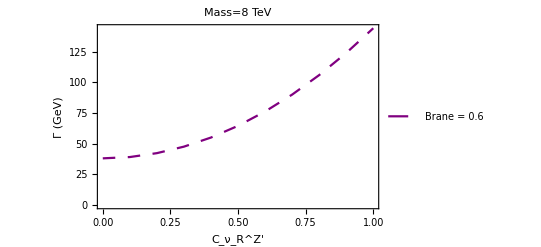

```mathematica
PlotZprimeDecayFixed806B=ListPlot[%%, Joined-> True,PlotStyle->{Purple,Dashing[Medium]},PlotLegends->{"Brane = 0.6"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass06Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 38.1629
0.1 | 39.2214
0.2 | 42.401
0.3 | 47.7017
0.4 | 55.1235
0.5 | 64.6663
0.6 | 76.3302
0.7 | 90.1152
0.8 | 106.021
0.9 | 124.048
1. | 144.197

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.6, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL06=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.6)
```

0.599871

```mathematica
Zprime5decayfixedmass06[CvR_]:=MassZprime5/(12π)(1/4(CvL06+CvR)^2+1/4(CvL06-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL06+CvR)^2-1/2(CvL06+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass06Table=Table[{Q[i],Zprime5decayfixedmass06[Q[i]]},{i,0,Npt}]
```

{{0.,23.8343},{0.1,24.4935},{0.2,26.4774},{0.3,29.786},{0.4,34.4192},{0.5,40.3772},{0.6,47.6599},{0.7,56.2672},{0.8,66.1993},{0.9,77.4561},{1.,90.0375}}

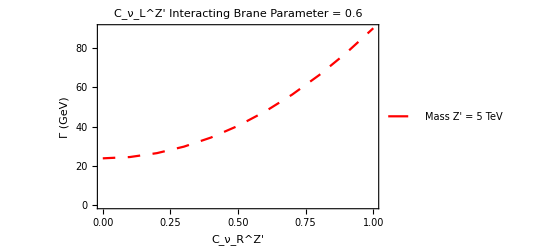

```mathematica
PlotZprimeDecayFixed506=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass Z' = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z' Interacting Brane Parameter = 0.6"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

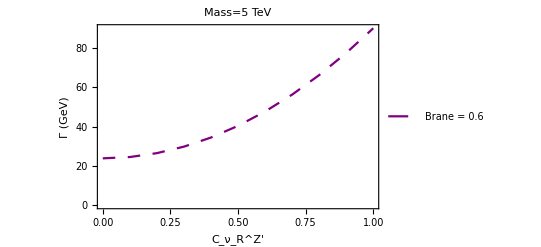

```mathematica
PlotZprimeDecayFixed506B=ListPlot[%%, Joined-> True,PlotStyle->{Purple,Dashing[Medium]},PlotLegends->{"Brane = 0.6"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass06Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 23.8343
0.1 | 24.4935
0.2 | 26.4774
0.3 | 29.786
0.4 | 34.4192
0.5 | 40.3772
0.6 | 47.6599
0.7 | 56.2672
0.8 | 66.1993
0.9 | 77.4561
1. | 90.0375

## OverLay

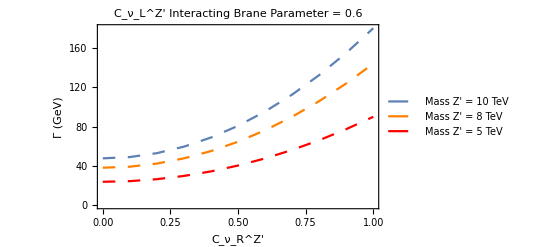

```mathematica
Show[PlotZprimeDecayFixed1006,PlotZprimeDecayFixed806,PlotZprimeDecayFixed506]
```

## OverLay 2

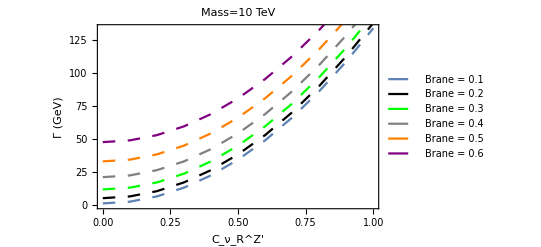

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B,PlotZprimeDecayFixed1005B,PlotZprimeDecayFixed1006B]
```

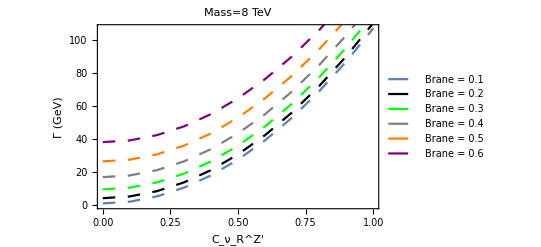

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B,PlotZprimeDecayFixed805B,PlotZprimeDecayFixed806B]
```

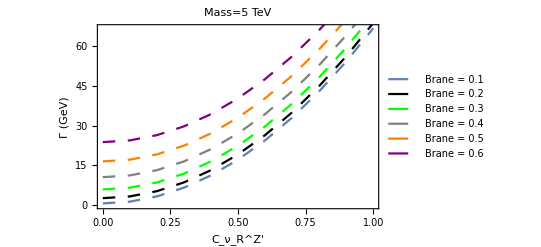

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B,PlotZprimeDecayFixed505B,PlotZprimeDecayFixed506B]
```